```mathematica
Exp[-x]
```

ⅇ^-x

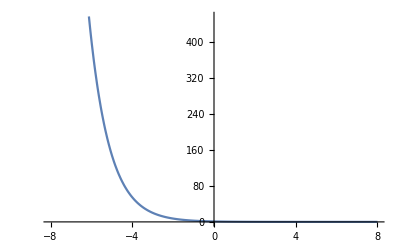

```mathematica
Plot[ⅇ^-x,{x,-8,8}]
```

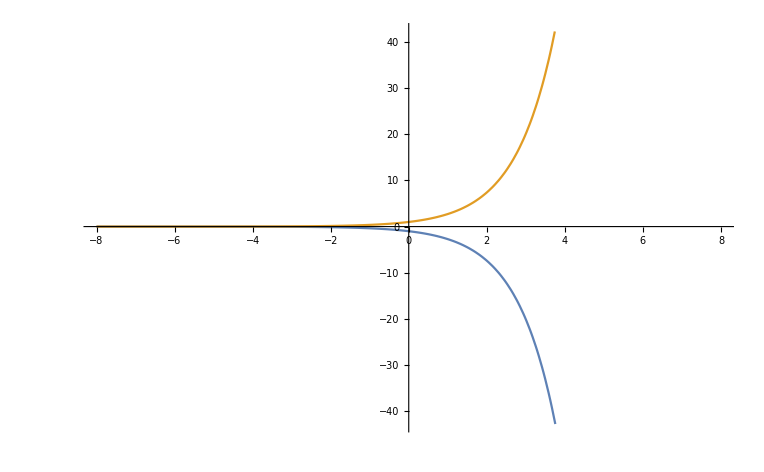

```mathematica
Plot[{-ⅇ^x,ⅇ^x},{x,-8,8}]
```

```mathematica
Integrate[Exp[x](-Exp[x]),{x,-∞,0}]
```

-1/2

```mathematica
Exp[0]
```

1

```mathematica
Integrate[Exp[x],{x,-∞,0}]
```

1

```mathematica
Integrate[-Exp[x],{x,-∞,0}]
```

-1

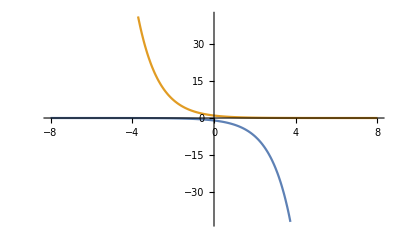

```mathematica
Plot[{-ⅇ^x,ⅇ^-x},{x,-8,8}]
```

```mathematica
Integrate[-Exp[x]Exp[-x],{x,-∞,∞}]
```

Integrate::idiv: Integral of -1 does not converge on {-∞,∞}.

∫_(-∞)^∞ -1ⅆx

```mathematica
1/(1+Exp[-x])
```

1/(1+ⅇ^-x)

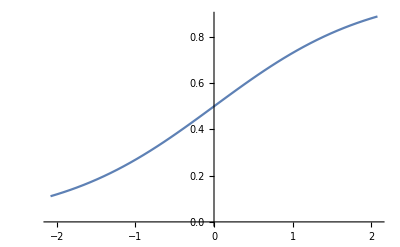

```mathematica
Plot[1/(1+ⅇ^-x),{x,-2.0794415416798357,2.0794415416798357}]
```

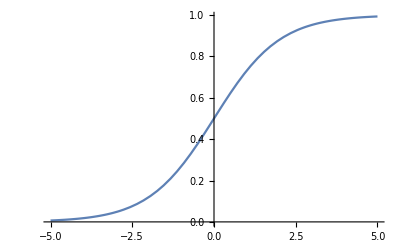

```mathematica
Plot[1/(1+ⅇ^-x),{x,-5,5}]
```

```mathematica
D[f[x],x]==(1-f[x])f[x]
```

f'[x]==(1-f[x]) f[x]

```mathematica
DSolve[f'[x]==(1-f[x]) f[x],{f[x]},{x}]
```

{{f[x]→ⅇ^x/(ⅇ^x+ⅇ^C[1])}}

```mathematica
1/(1+ⅇ^x)
```

1/(1+ⅇ^x)

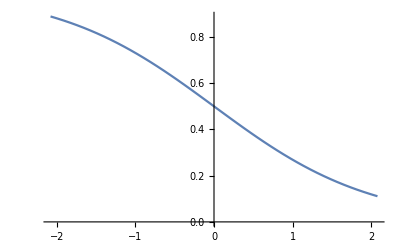

```mathematica
Plot[1/(1+ⅇ^x),{x,-2.0794415416798357,2.0794415416798357}]
```

```mathematica
Integrate[1/(1+ⅇ^x)1/(1+ⅇ^-x),{x,-∞,∞}]
```

1

```mathematica
Integrate[1/(1+ⅇ^x)1/(1+ⅇ^-x),{x,0,∞}]
```

1/2

```mathematica
Integrate[1/(1+ⅇ^x)1/(1+ⅇ^-x),x]
```

-1/(1+ⅇ^x)

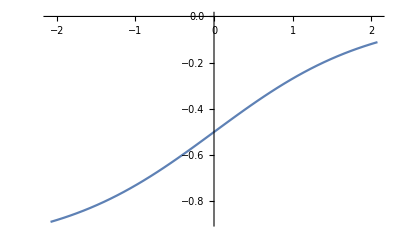

```mathematica
Plot[-1/(1+ⅇ^x),{x,-2.0794415416798357,2.0794415416798357}]
```

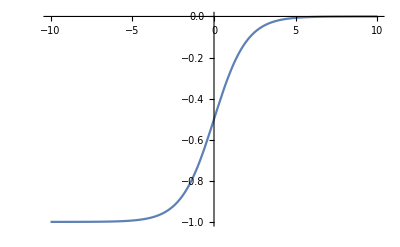

```mathematica
Plot[-1/(1+ⅇ^x),{x,-10,10}]
```

```mathematica
LaplaceTransform[Exp[x],x,s]
```

1/(-1+s)

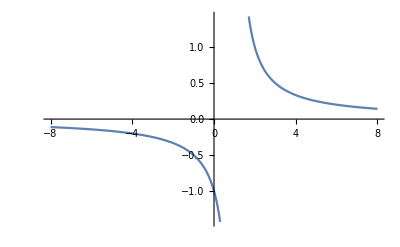

```mathematica
Plot[1/(-1+s),{s,-8,8}]
```

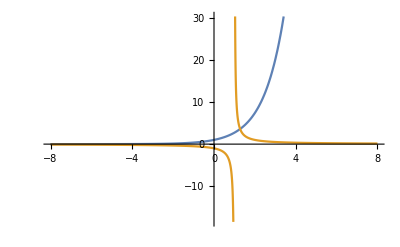

```mathematica
Plot[{Exp[s],1/(-1+s)},{s,-8,8}]
```

```mathematica
HeavisideTheta[x]
```

HeavisideTheta[x]

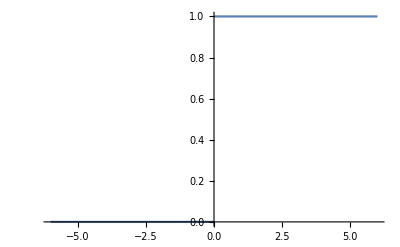

```mathematica
Plot[HeavisideTheta[x],{x,-6.,6.}]
```

```mathematica
LaplaceTransform[HeavisideTheta[x],x,s]
```

1/s

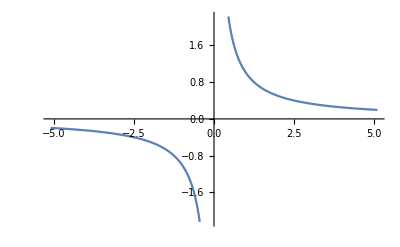

```mathematica
Plot[1/s,{s,-5.1,5.1}]
```

```mathematica
Ramp[x]
```

Ramp[x]

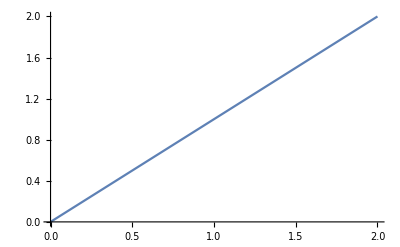

```mathematica
Plot[Ramp[x],{x,0,2}]
```

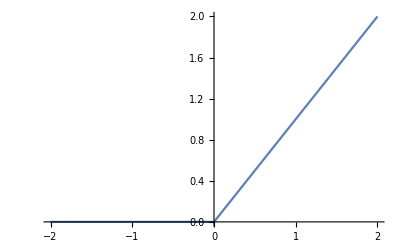

```mathematica
Plot[Ramp[x],{x,-2,2}]
```

```mathematica
lenetModel=NetModel["LeNet Trained on MNIST Data"]
```

NetChain[<>]

```mathematica
lenetModel[{-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{3,9,8,4}

```mathematica
trainingData=ResourceData["MNIST","TrainingData"];
testData=ResourceData["MNIST","TestData"];
```

```mathematica
NetTrain[NetModel["LeNet"],trainingData,ValidationSet->testData]
```

```mathematica
LaplaceTransform[UnitStep[x],x,s]
```

1/s

```mathematica
Plot[1/s,{s,-5.1,5.1}]
```

-Graphics-

```mathematica
lenetModel=NetModel["LeNet Trained on MNIST Data"]
```

NetChain[<>]

```mathematica
NetExtract[lenetModel,"Properties"]
```

Missing[NotPresent,{Properties}]

```mathematica
NetExtract[lenetModel,All]
```

{ConvolutionLayer[<>],ElementwiseLayer[<>],PoolingLayer[<>],ConvolutionLayer[<>],ElementwiseLayer[<>],PoolingLayer[<>],FlattenLayer[<>],LinearLayer[<>],ElementwiseLayer[<>],LinearLayer[<>],SoftmaxLayer[<>]}

```mathematica
layer=NetExtract[lenetModel,-1]
```

SoftmaxLayer[<>]

```mathematica
layer[{1,2,5,2,4,7,4,3,5,3}]
```

{0.00174213,0.00473559,0.0951169,0.00473559,0.0349916,0.702824,0.0349916,0.0128727,0.0951169,0.0128727}

```mathematica
Total[{0.001742127351462841,0.004735592752695084,0.09511692821979523,0.004735592752695084,0.034991562366485596,0.7028242945671082,0.034991562366485596,0.012872676365077496,0.09511692821979523,0.012872676365077496}]
```

1.

```mathematica
linear=LinearLayer[3,"Input"->2]
```

LinearLayer[<>]

```mathematica
linear[{2,3}]
```

LinearLayer::nninit: Cannot evaluate net: unspecified value for array "Weights".

$Failed

```mathematica
initializedLinear=NetInitialize[linear]
```

LinearLayer[<>]

```mathematica
initializedLinear[{2,3}]
```

{-0.487702,-2.18997,-1.75808}

```mathematica
NetExtract[initializedLinear,"Weights"]
```

NumericArray[…]

```mathematica
NetExtract[initializedLinear,"Biases"]
```

NumericArray[…]

```mathematica
?*Layer
```

```mathematica
imageenc=NetEncoder[{"Image",{12,12},"ColorSpace"->"Grayscale"}]
```

NetEncoder[<>]

```mathematica
imageenc[-Graphics-]
```

{{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,0.,0.,0.,0.,0.,1.,1.,1.},{1.,1.,1.,0.,0.,0.,0.,0.,0.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,0.,0.,0.,1.,1.,1.},{1.,1.,1.,1.,0.,0.,0.,0.,0.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,1.,1.},{1.,1.,0.,1.,1.,1.,1.,1.,0.,0.,1.,1.},{1.,1.,0.,0.,1.,1.,0.,0.,0.,1.,1.,1.},{1.,1.,1.,1.,0.,0.,0.,0.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}}

```mathematica
Normal[Out[17]]
```

{{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,0.,0.,0.,0.,0.,1.,1.,1.},{1.,1.,1.,0.,0.,0.,0.,0.,0.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,0.,0.,0.,1.,1.,1.},{1.,1.,1.,1.,0.,0.,0.,0.,0.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,1.,1.},{1.,1.,0.,1.,1.,1.,1.,1.,0.,0.,1.,1.},{1.,1.,0.,0.,1.,1.,0.,0.,0.,1.,1.,1.},{1.,1.,1.,1.,0.,0.,0.,0.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}}

```mathematica
mnistEncoder=NetEncoder[{"Image",{28,28},"ColorSpace"->"Grayscale"}]
```

NetEncoder[<>]

```mathematica
trainingData[[1,1]]
```

Part::partd: Part specification trainingData⟦1,1⟧ is longer than depth of object.

trainingData⟦1,1⟧

```mathematica
NetExtract[lenetModel,{All,"Function"}]
```

{Missing[NotPresent,{All,Function}],Ramp,Max,Missing[NotPresent,{All,Function}],Ramp,Max,Missing[NotPresent,{All,Function}],Missing[NotPresent,{All,Function}],Ramp,Missing[NotPresent,{All,Function}],Missing[NotPresent,{All,Function}]}

```mathematica
NetExtract[lenetModel,{All,"Weights"}]
```

{NumericArray[…],Missing[NotPresent,{All,Weights}],Missing[NotPresent,{All,Weights}],NumericArray[…],Missing[NotPresent,{All,Weights}],Missing[NotPresent,{All,Weights}],Missing[NotPresent,{All,Weights}],NumericArray[<500,800>, Real32],Missing[NotPresent,{All,Weights}],NumericArray[…],Missing[NotPresent,{All,Weights}]}

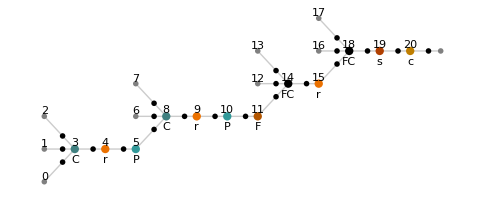

```mathematica
NetInformation[lenetModel,"MXNetNodeGraphPlot"]
```

```mathematica
NetInformation[lenetModel,"FullSummaryGraphic"]
```

-Graphics-

```mathematica
NetInformation[lenetModel,"LayersList"]
```

{ConvolutionLayer[<>],ElementwiseLayer[<>],PoolingLayer[<>],ConvolutionLayer[<>],ElementwiseLayer[<>],PoolingLayer[<>],FlattenLayer[<>],LinearLayer[<>],ElementwiseLayer[<>],LinearLayer[<>],SoftmaxLayer[<>]}

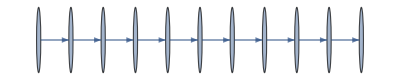

```mathematica
NetInformation[lenetModel,"LayersGraph"]
```

```mathematica
NetModel["Dilated ResNet-105 Trained on Cityscapes Data"]
```

NetGraph[<>]

```mathematica
city=Out[27]
```

NetGraph[<>]

```mathematica
NetInformation[city,"Layers"]
```

<|{convolution0}→ConvolutionLayer[<>],{batchnorm0}→BatchNormalizationLayer[<>],{relu0}→ElementwiseLayer[<>],{convolution1}→ConvolutionLayer[<>],{batchnorm1}→BatchNormalizationLayer[<>],{relu1}→ElementwiseLayer[<>],{convolution2}→ConvolutionLayer[<>],{batchnorm2}→BatchNormalizationLayer[<>],{relu2}→ElementwiseLayer[<>],{convolution3}→ConvolutionLayer[<>],{batchnorm3}→BatchNormalizationLayer[<>],{relu3}→ElementwiseLayer[<>],{convolution4}→ConvolutionLayer[<>],{batchnorm4}→BatchNormalizationLayer[<>],{relu4}→ElementwiseLayer[<>],{convolution5}→ConvolutionLayer[<>],{batchnorm5}→BatchNormalizationLayer[<>],{convolution6}→ConvolutionLayer[<>],{batchnorm6}→BatchNormalizationLayer[<>],{elemwise_add0}→ThreadingLayer[<>],{relu5}→ElementwiseLayer[<>],{convolution7}→ConvolutionLayer[<>],{batchnorm7}→BatchNormalizationLayer[<>],{relu6}→ElementwiseLayer[<>],{convolution8}→ConvolutionLayer[<>],{batchnorm8}→BatchNormalizationLayer[<>],{relu7}→ElementwiseLayer[<>],{convolution9}→ConvolutionLayer[<>],{batchnorm9}→BatchNormalizationLayer[<>],{elemwise_add1}→ThreadingLayer[<>],{relu8}→ElementwiseLayer[<>],{convolution10}→ConvolutionLayer[<>],{batchnorm10}→BatchNormalizationLayer[<>],{relu9}→ElementwiseLayer[<>],{convolution11}→ConvolutionLayer[<>],{batchnorm11}→BatchNormalizationLayer[<>],{relu10}→ElementwiseLayer[<>],{convolution12}→ConvolutionLayer[<>],{batchnorm12}→BatchNormalizationLayer[<>],{elemwise_add2}→ThreadingLayer[<>],{relu11}→ElementwiseLayer[<>],{convolution13}→ConvolutionLayer[<>],{batchnorm13}→BatchNormalizationLayer[<>],{relu12}→ElementwiseLayer[<>],{convolution14}→ConvolutionLayer[<>],{batchnorm14}→BatchNormalizationLayer[<>],{relu13}→ElementwiseLayer[<>],{convolution15}→ConvolutionLayer[<>],{batchnorm15}→BatchNormalizationLayer[<>],{convolution16}→ConvolutionLayer[<>],{batchnorm16}→BatchNormalizationLayer[<>],{elemwise_add3}→ThreadingLayer[<>],{relu14}→ElementwiseLayer[<>],{convolution17}→ConvolutionLayer[<>],{batchnorm17}→BatchNormalizationLayer[<>],{relu15}→ElementwiseLayer[<>],{convolution18}→ConvolutionLayer[<>],{batchnorm18}→BatchNormalizationLayer[<>],{relu16}→ElementwiseLayer[<>],{convolution19}→ConvolutionLayer[<>],{batchnorm19}→BatchNormalizationLayer[<>],{elemwise_add4}→ThreadingLayer[<>],{relu17}→ElementwiseLayer[<>],{convolution20}→ConvolutionLayer[<>],{batchnorm20}→BatchNormalizationLayer[<>],{relu18}→ElementwiseLayer[<>],{convolution21}→ConvolutionLayer[<>],{batchnorm21}→BatchNormalizationLayer[<>],{relu19}→ElementwiseLayer[<>],{convolution22}→ConvolutionLayer[<>],{batchnorm22}→BatchNormalizationLayer[<>],{elemwise_add5}→ThreadingLayer[<>],{relu20}→ElementwiseLayer[<>],{convolution23}→ConvolutionLayer[<>],{batchnorm23}→BatchNormalizationLayer[<>],{relu21}→ElementwiseLayer[<>],{convolution24}→ConvolutionLayer[<>],{batchnorm24}→BatchNormalizationLayer[<>],{relu22}→ElementwiseLayer[<>],{convolution25}→ConvolutionLayer[<>],{batchnorm25}→BatchNormalizationLayer[<>],{elemwise_add6}→ThreadingLayer[<>],{relu23}→ElementwiseLayer[<>],{convolution26}→ConvolutionLayer[<>],{batchnorm26}→BatchNormalizationLayer[<>],{relu24}→ElementwiseLayer[<>],{convolution27}→ConvolutionLayer[<>],{batchnorm27}→BatchNormalizationLayer[<>],{relu25}→ElementwiseLayer[<>],{convolution28}→ConvolutionLayer[<>],{batchnorm28}→BatchNormalizationLayer[<>],{convolution29}→ConvolutionLayer[<>],{batchnorm29}→BatchNormalizationLayer[<>],{elemwise_add7}→ThreadingLayer[<>],{relu26}→ElementwiseLayer[<>],{convolution30}→ConvolutionLayer[<>],{batchnorm30}→BatchNormalizationLayer[<>],{relu27}→ElementwiseLayer[<>],{convolution31}→ConvolutionLayer[<>],{batchnorm31}→BatchNormalizationLayer[<>],{relu28}→ElementwiseLayer[<>],{convolution32}→ConvolutionLayer[<>],{batchnorm32}→BatchNormalizationLayer[<>],{elemwise_add8}→ThreadingLayer[<>],{relu29}→ElementwiseLayer[<>],{convolution33}→ConvolutionLayer[<>],{batchnorm33}→BatchNormalizationLayer[<>],{relu30}→ElementwiseLayer[<>],{convolution34}→ConvolutionLayer[<>],{batchnorm34}→BatchNormalizationLayer[<>],{relu31}→ElementwiseLayer[<>],{convolution35}→ConvolutionLayer[<>],{batchnorm35}→BatchNormalizationLayer[<>],{elemwise_add9}→ThreadingLayer[<>],{relu32}→ElementwiseLayer[<>],{convolution36}→ConvolutionLayer[<>],{batchnorm36}→BatchNormalizationLayer[<>],{relu33}→ElementwiseLayer[<>],{convolution37}→ConvolutionLayer[<>],{batchnorm37}→BatchNormalizationLayer[<>],{relu34}→ElementwiseLayer[<>],{convolution38}→ConvolutionLayer[<>],{batchnorm38}→BatchNormalizationLayer[<>],{elemwise_add10}→ThreadingLayer[<>],{relu35}→ElementwiseLayer[<>],{convolution39}→ConvolutionLayer[<>],{batchnorm39}→BatchNormalizationLayer[<>],{relu36}→ElementwiseLayer[<>],{convolution40}→ConvolutionLayer[<>],{batchnorm40}→BatchNormalizationLayer[<>],{relu37}→ElementwiseLayer[<>],{convolution41}→ConvolutionLayer[<>],{batchnorm41}→BatchNormalizationLayer[<>],{elemwise_add11}→ThreadingLayer[<>],{relu38}→ElementwiseLayer[<>],{convolution42}→ConvolutionLayer[<>],{batchnorm42}→BatchNormalizationLayer[<>],{relu39}→ElementwiseLayer[<>],{convolution43}→ConvolutionLayer[<>],{batchnorm43}→BatchNormalizationLayer[<>],{relu40}→ElementwiseLayer[<>],{convolution44}→ConvolutionLayer[<>],{batchnorm44}→BatchNormalizationLayer[<>],{elemwise_add12}→ThreadingLayer[<>],{relu41}→ElementwiseLayer[<>],{convolution45}→ConvolutionLayer[<>],{batchnorm45}→BatchNormalizationLayer[<>],{relu42}→ElementwiseLayer[<>],{convolution46}→ConvolutionLayer[<>],{batchnorm46}→BatchNormalizationLayer[<>],{relu43}→ElementwiseLayer[<>],{convolution47}→ConvolutionLayer[<>],{batchnorm47}→BatchNormalizationLayer[<>],{elemwise_add13}→ThreadingLayer[<>],{relu44}→ElementwiseLayer[<>],{convolution48}→ConvolutionLayer[<>],{batchnorm48}→BatchNormalizationLayer[<>],{relu45}→ElementwiseLayer[<>],{convolution49}→ConvolutionLayer[<>],{batchnorm49}→BatchNormalizationLayer[<>],{relu46}→ElementwiseLayer[<>],{convolution50}→ConvolutionLayer[<>],{batchnorm50}→BatchNormalizationLayer[<>],{elemwise_add14}→ThreadingLayer[<>],{relu47}→ElementwiseLayer[<>],{convolution51}→ConvolutionLayer[<>],{batchnorm51}→BatchNormalizationLayer[<>],{relu48}→ElementwiseLayer[<>],{convolution52}→ConvolutionLayer[<>],{batchnorm52}→BatchNormalizationLayer[<>],{relu49}→ElementwiseLayer[<>],{convolution53}→ConvolutionLayer[<>],{batchnorm53}→BatchNormalizationLayer[<>],{elemwise_add15}→ThreadingLayer[<>],{relu50}→ElementwiseLayer[<>],{convolution54}→ConvolutionLayer[<>],{batchnorm54}→BatchNormalizationLayer[<>],{relu51}→ElementwiseLayer[<>],{convolution55}→ConvolutionLayer[<>],{batchnorm55}→BatchNormalizationLayer[<>],{relu52}→ElementwiseLayer[<>],{convolution56}→ConvolutionLayer[<>],{batchnorm56}→BatchNormalizationLayer[<>],{elemwise_add16}→ThreadingLayer[<>],{relu53}→ElementwiseLayer[<>],{convolution57}→ConvolutionLayer[<>],{batchnorm57}→BatchNormalizationLayer[<>],{relu54}→ElementwiseLayer[<>],{convolution58}→ConvolutionLayer[<>],{batchnorm58}→BatchNormalizationLayer[<>],{relu55}→ElementwiseLayer[<>],{convolution59}→ConvolutionLayer[<>],{batchnorm59}→BatchNormalizationLayer[<>],{elemwise_add17}→ThreadingLayer[<>],{relu56}→ElementwiseLayer[<>],{convolution60}→ConvolutionLayer[<>],{batchnorm60}→BatchNormalizationLayer[<>],{relu57}→ElementwiseLayer[<>],{convolution61}→ConvolutionLayer[<>],{batchnorm61}→BatchNormalizationLayer[<>],{relu58}→ElementwiseLayer[<>],{convolution62}→ConvolutionLayer[<>],{batchnorm62}→BatchNormalizationLayer[<>],{elemwise_add18}→ThreadingLayer[<>],{relu59}→ElementwiseLayer[<>],{convolution63}→ConvolutionLayer[<>],{batchnorm63}→BatchNormalizationLayer[<>],{relu60}→ElementwiseLayer[<>],{convolution64}→ConvolutionLayer[<>],{batchnorm64}→BatchNormalizationLayer[<>],{relu61}→ElementwiseLayer[<>],{convolution65}→ConvolutionLayer[<>],{batchnorm65}→BatchNormalizationLayer[<>],{elemwise_add19}→ThreadingLayer[<>],{relu62}→ElementwiseLayer[<>],{convolution66}→ConvolutionLayer[<>],{batchnorm66}→BatchNormalizationLayer[<>],{relu63}→ElementwiseLayer[<>],{convolution67}→ConvolutionLayer[<>],{batchnorm67}→BatchNormalizationLayer[<>],{relu64}→ElementwiseLayer[<>],{convolution68}→ConvolutionLayer[<>],{batchnorm68}→BatchNormalizationLayer[<>],{elemwise_add20}→ThreadingLayer[<>],{relu65}→ElementwiseLayer[<>],{convolution69}→ConvolutionLayer[<>],{batchnorm69}→BatchNormalizationLayer[<>],{relu66}→ElementwiseLayer[<>],{convolution70}→ConvolutionLayer[<>],{batchnorm70}→BatchNormalizationLayer[<>],{relu67}→ElementwiseLayer[<>],{convolution71}→ConvolutionLayer[<>],{batchnorm71}→BatchNormalizationLayer[<>],{elemwise_add21}→ThreadingLayer[<>],{relu68}→ElementwiseLayer[<>],{convolution72}→ConvolutionLayer[<>],{batchnorm72}→BatchNormalizationLayer[<>],{relu69}→ElementwiseLayer[<>],{convolution73}→ConvolutionLayer[<>],{batchnorm73}→BatchNormalizationLayer[<>],{relu70}→ElementwiseLayer[<>],{convolution74}→ConvolutionLayer[<>],{batchnorm74}→BatchNormalizationLayer[<>],{elemwise_add22}→ThreadingLayer[<>],{relu71}→ElementwiseLayer[<>],{convolution75}→ConvolutionLayer[<>],{batchnorm75}→BatchNormalizationLayer[<>],{relu72}→ElementwiseLayer[<>],{convolution76}→ConvolutionLayer[<>],{batchnorm76}→BatchNormalizationLayer[<>],{relu73}→ElementwiseLayer[<>],{convolution77}→ConvolutionLayer[<>],{batchnorm77}→BatchNormalizationLayer[<>],{elemwise_add23}→ThreadingLayer[<>],{relu74}→ElementwiseLayer[<>],{convolution78}→ConvolutionLayer[<>],{batchnorm78}→BatchNormalizationLayer[<>],{relu75}→ElementwiseLayer[<>],{convolution79}→ConvolutionLayer[<>],{batchnorm79}→BatchNormalizationLayer[<>],{relu76}→ElementwiseLayer[<>],{convolution80}→ConvolutionLayer[<>],{batchnorm80}→BatchNormalizationLayer[<>],{elemwise_add24}→ThreadingLayer[<>],{relu77}→ElementwiseLayer[<>],{convolution81}→ConvolutionLayer[<>],{batchnorm81}→BatchNormalizationLayer[<>],{relu78}→ElementwiseLayer[<>],{convolution82}→ConvolutionLayer[<>],{batchnorm82}→BatchNormalizationLayer[<>],{relu79}→ElementwiseLayer[<>],{convolution83}→ConvolutionLayer[<>],{batchnorm83}→BatchNormalizationLayer[<>],{elemwise_add25}→ThreadingLayer[<>],{relu80}→ElementwiseLayer[<>],{convolution84}→ConvolutionLayer[<>],{batchnorm84}→BatchNormalizationLayer[<>],{relu81}→ElementwiseLayer[<>],{convolution85}→ConvolutionLayer[<>],{batchnorm85}→BatchNormalizationLayer[<>],{relu82}→ElementwiseLayer[<>],{convolution86}→ConvolutionLayer[<>],{batchnorm86}→BatchNormalizationLayer[<>],{elemwise_add26}→ThreadingLayer[<>],{relu83}→ElementwiseLayer[<>],{convolution87}→ConvolutionLayer[<>],{batchnorm87}→BatchNormalizationLayer[<>],{relu84}→ElementwiseLayer[<>],{convolution88}→ConvolutionLayer[<>],{batchnorm88}→BatchNormalizationLayer[<>],{relu85}→ElementwiseLayer[<>],{convolution89}→ConvolutionLayer[<>],{batchnorm89}→BatchNormalizationLayer[<>],{elemwise_add27}→ThreadingLayer[<>],{relu86}→ElementwiseLayer[<>],{convolution90}→ConvolutionLayer[<>],{batchnorm90}→BatchNormalizationLayer[<>],{relu87}→ElementwiseLayer[<>],{convolution91}→ConvolutionLayer[<>],{batchnorm91}→BatchNormalizationLayer[<>],{relu88}→ElementwiseLayer[<>],{convolution92}→ConvolutionLayer[<>],{batchnorm92}→BatchNormalizationLayer[<>],{elemwise_add28}→ThreadingLayer[<>],{relu89}→ElementwiseLayer[<>],{convolution93}→ConvolutionLayer[<>],{batchnorm93}→BatchNormalizationLayer[<>],{relu90}→ElementwiseLayer[<>],{convolution94}→ConvolutionLayer[<>],{batchnorm94}→BatchNormalizationLayer[<>],{relu91}→ElementwiseLayer[<>],{convolution95}→ConvolutionLayer[<>],{batchnorm95}→BatchNormalizationLayer[<>],{elemwise_add29}→ThreadingLayer[<>],{relu92}→ElementwiseLayer[<>],{convolution96}→ConvolutionLayer[<>],{batchnorm96}→BatchNormalizationLayer[<>],{relu93}→ElementwiseLayer[<>],{convolution97}→ConvolutionLayer[<>],{batchnorm97}→BatchNormalizationLayer[<>],{relu94}→ElementwiseLayer[<>],{convolution98}→ConvolutionLayer[<>],{batchnorm98}→BatchNormalizationLayer[<>],{convolution99}→ConvolutionLayer[<>],{batchnorm99}→BatchNormalizationLayer[<>],{elemwise_add30}→ThreadingLayer[<>],{relu95}→ElementwiseLayer[<>],{convolution100}→ConvolutionLayer[<>],{batchnorm100}→BatchNormalizationLayer[<>],{relu96}→ElementwiseLayer[<>],{convolution101}→ConvolutionLayer[<>],{batchnorm101}→BatchNormalizationLayer[<>],{relu97}→ElementwiseLayer[<>],{convolution102}→ConvolutionLayer[<>],{batchnorm102}→BatchNormalizationLayer[<>],{elemwise_add31}→ThreadingLayer[<>],{relu98}→ElementwiseLayer[<>],{convolution103}→ConvolutionLayer[<>],{batchnorm103}→BatchNormalizationLayer[<>],{relu99}→ElementwiseLayer[<>],{convolution104}→ConvolutionLayer[<>],{batchnorm104}→BatchNormalizationLayer[<>],{relu100}→ElementwiseLayer[<>],{convolution105}→ConvolutionLayer[<>],{batchnorm105}→BatchNormalizationLayer[<>],{elemwise_add32}→ThreadingLayer[<>],{relu101}→ElementwiseLayer[<>],{convolution106}→ConvolutionLayer[<>],{batchnorm106}→BatchNormalizationLayer[<>],{relu102}→ElementwiseLayer[<>],{convolution107}→ConvolutionLayer[<>],{batchnorm107}→BatchNormalizationLayer[<>],{relu103}→ElementwiseLayer[<>],{convolution108}→ConvolutionLayer[<>],{broadcast_add0,1}→ConstantArrayLayer[<>],{broadcast_add0,2}→ReplicateLayer[<>],{broadcast_add0,3}→ThreadingLayer[<>],{deconvolution0}→DeconvolutionLayer[<>],{transpose}→TransposeLayer[<>],{softmax0}→SoftmaxLayer[<>]|>

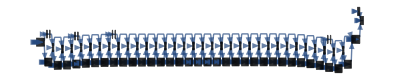

```mathematica
NetInformation[city,"LayersGraph"]
```

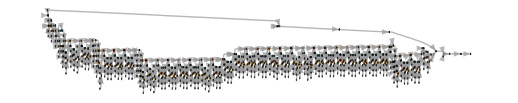

```mathematica
NetInformation[city,"MXNetNodeGraph"]
```

```mathematica
NetInformation[city,"MXNetNodeGraphPlot"]
```

graph size 907 exceeded $MaxGraphPlotNodes